# Cuaderno de prácticas de Matemática Discreta

## Práctica 7

## Grado en Ingeniería Informática Curso 2023/2024

## Datos personales :

Apellidos y nombre: Carrasco Vico, Juan
	DNI: 11111111 0
	Fecha de nacimiento: 25/03/2005
	Grupo de teoría: A
	Grupo de prácticas: 1

## Ejercicio 8.1: Sea A={a,b,c,d,e}, consideremos la relación binaria R = {(a,b)(b,c),(d,e)}

```mathematica
AnalisisRB[A_,R_]:=Module[{},falloReflexiva={};
Do[If[MemberQ[R,{A[[n]],A[[n]]}],Null,AppendTo[falloReflexiva,A[[n]]]],{n,Length[A]}];
falloSimetrica={};
Do[If[MemberQ[R,{R[[m,2]],R[[m,1]]}],Null,AppendTo[falloSimetrica,{R[[m,2]],R[[m,1]]}]],{m,Length[R]}];
falloTransitiva={};
Do[Do[If[R[[p,1]]==R[[q,2]],If[MemberQ[R,{R[[q,1]],R[[p,2]]}],Null,AppendTo[falloTransitiva,{{R[[q,1]],R[[q,2]]},{R[[p,1]],R[[p,2]]}}]]];,{q,Length[R]}];,{p,Length[R]}];
falloAntisimetrica={};
Do[If[MemberQ[R,{R[[r,2]],R[[r,1]]}]&&!(ToString[R[[r,1]]]==ToString[R[[r,2]]]),AppendTo[falloAntisimetrica,{R[[r,1]],R[[r,2]]}];];,{r,Length[R]}];
If[falloReflexiva=={},Print["R es reflexiva"],Print["R no es reflexiva, falla en los elementos: ",falloReflexiva]];
If[falloSimetrica=={},Print["R es simétrica"],Print["R no es simétrica, falla en los pares: ",falloSimetrica]];
If[falloTransitiva=={},Print["R es transitiva"],Print["R no es transitiva, falla en los pares: ",falloTransitiva]];
If[falloAntisimetrica=={},Print["R es antisimétrica"],Print["R no es antisimétrica, falla en los pares: ",falloAntisimetrica]];
If[Union[falloReflexiva,falloSimetrica,falloTransitiva]=={},Print["R es una relación de equivalencia"],Print["R no es relación de equivalencia"]];
If[Union[falloReflexiva,falloAntisimetrica,falloTransitiva]=={},Print["R es una relación de orden"],Print["R no es relación de orden"]];];
```

### a)Completar la relación binaria R para que sea una relación de orden total

```mathematica
A = {a,b,c,d,e};
R= {{a,a},{a,b},{a,c},{a,d},{a,e},{b,b},{b,c},{b,d},{b,e},{c,c},{c,d},{c,e},{d,d},{d,e},{e,e}};
AnalisisRB[A,R]
```

R es reflexiva

R no es simétrica, falla en los pares: {{b,a},{c,a},{d,a},{e,a},{c,b},{d,b},{e,b},{d,c},{e,c},{e,d}}

R es transitiva

R es antisimétrica

R no es relación de equivalencia

R es una relación de orden

### b) Completar la relación binaria R para que sea reflexiva y transitiva, pero no sea simétrica y antisimétrica.

```mathematica
A = {a,b,c,d,e};
R= {{a,a},{a,b},{a,c},{a,d},{a,e},
   {b,a},{b,b},{b,c},{b,d},{b,e},
   {c,c},{c,d},{c,e},
   {d,d},{d,e},
   {e,e}};
AnalisisRB[A,R]
```

R es reflexiva

R no es simétrica, falla en los pares: {{c,a},{d,a},{e,a},{c,b},{d,b},{e,b},{d,c},{e,c},{e,d}}

R es transitiva

R no es antisimétrica, falla en los pares: {{a,b},{b,a}}

R no es relación de equivalencia

R no es relación de orden

## Ejercicio 8.4: Calcular diagrama de orden de P{a,b,c}

Diagrama de orden:

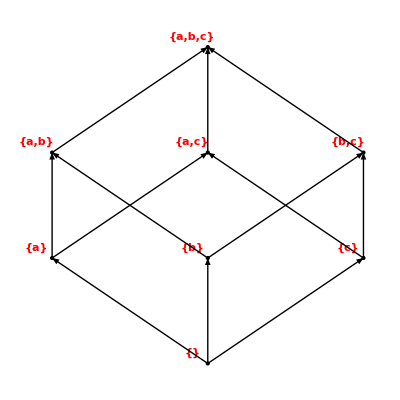

```mathematica
Clear[A,R]
A:=Subsets[{"a","b","c"}]
R:={}
For[i=1,i<Length[A]+1,i++,
	For[j=1,j<Length[A]+1,j++,
		If[Intersection[A[[i]],A[[j]]]==A[[i]],
			AppendTo[R,{A[[i]],A[[j]]}]]]]
A:=Subsets[{"a","b","c"}]
R:={}
For[i=1,i<Length[A]+1,i++,
	For[j=1,j<Length[A]+1,j++,
		If[Intersection[A[[i]],A[[j]]]==A[[i]],
			AppendTo[R,{A[[i]],A[[j]]}]
		]
	]
]
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
	Do[minimal=True;
		Do[If[Intersection[{{B[[m1]],B[[n1]]}},R]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
		If[minimal,AppendTo[minimales,B[[n1]]];
		tabla[[t1]]={nivel,B[[n1]],0};
		t1++;];
		,{n1,1,Length[B]}];
	B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
R=Complement[R,R1];
R1={};
Do[
	Do[
		If[Length[Intersection[R,{{R[[k1,1]],A[[j1]]},{A[[j1]],R[[k1,2]]}}]]==2,R1=Union[R1,{R[[k1]]}];];
		,{j1,1,Length[A]}]
	,{k1,1,Length[R]}];
R=Complement[R,R1];
puntos={};t1=0;
Do[cont=0;
	Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
	Do[t1++;
		puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
		tabla[[t1,3]]=k1-(cont/2);
		,{k1,1,cont}]
,{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
	Do[AppendTo[puntos,Arrow[{Coord[R[[t1,1]]],Coord[R[[t1,2]]]}]];
	,{t1,1,Length[R]}];
	Print["Diagrama de orden:"]
Show[Graphics[puntos],AspectRatio->1,Background->None]
```

## Ejercicio 8.9: En el conjunto A = {1, 2, 3, 4} se establece la relación R= {{1, 1}, {2, 2}, {2, 3}, {2, 4}, {3, 2}, {3, 3}, {3, 4}, {4, 2}, {4, 3}, {4, 4}}. Justifica que es una relación de equivalencia y calcular el conjunto cociente.

```mathematica
Clear[A,R]
A:={1,2,3,4};
R:={{1,1},{2,2},{2,3},{2,4},{3,2},{3,3},{3,4},{4,2},{4,3},{4,4}};

AnalisisRB[A,R]
```

R es reflexiva

R es simétrica

R es transitiva

R no es antisimétrica, falla en los pares: {{2,3},{2,4},{3,2},{3,4},{4,2},{4,3}}

R es una relación de equivalencia

R no es relación de orden

```mathematica
COCIENTE[A_,R_]:=Module[{CONTADORi,CONTADORj,anadir},cociente={{A[[1]]}};
Do[anadir=True;
Do[If[Intersection[{{A[[CONTADORi]],cociente[[CONTADORj]][[1]]}},R]≠{},AppendTo[cociente[[CONTADORj]],A[[CONTADORi]]];
anadir=False;
Break[];];,{CONTADORj,1,Length[cociente]}];
If[anadir,AppendTo[cociente,{A[[CONTADORi]]}];];,{CONTADORi,2,Length[A]}];
cociente];

COCIENTE[A,R]
```

{{1},{2,3,4}}

## Ejercicio 8.14: Sea X={a,b,c,d,e,f} junto a R...

```mathematica
Clear[A,R,a,b,c,d,e,f]
X={"a","b","c","d","e","f"};
Y={"b","f","e"};
Z={"c","a","e","d"};
R={
{"f","f"},{"f","e"},{"f","d"},{"f","c"},{"f","b"},{"f","a"},
{"e","e"},{"e","b"},{"e","c"},{"e","a"},
{"b","b"},{"b","a"},
{"d","d"},{"d","b"},{"d","a"},
{"a","a"},{"c","c"}
};
```

### a)Cotas superiores e inferiores de Y y de Z ¿Existen supremo e ínfimo?

```mathematica
COTASSUPERIORES[A_,B_,R_]:=Module[{cotassuperiores,csuper,n,m,supremo},cotassuperiores={};
Do[csuper=True;
Do[If[Intersection[{{B[[m]],A[[n]]}},R]=={},csuper=False;],{m,1,Length[B]}];
If[csuper,AppendTo[cotassuperiores,A[[n]]]];,{n,1,Length[A]}];
If[cotassuperiores=={},Print["No hay cotas superiores"],Print["Las cotas superiores son: ",cotassuperiores]];
supremo = {};
Do[
mini = True;
Do[
If[Intersection[{{cotassuperiores[[n]],cotassuperiores[[m]]}},R]=={},mini=False];
,{m,1,Length[cotassuperiores]}];
If[mini, AppendTo[supremo,cotassuperiores[[n]]];]
,{n,1,Length[cotassuperiores]}
];
If[supremo=={},Print["No hay supremo"], Print["El supremo es: ", supremo]]]

COTASINFERIORES[A_,B_,R_]:=Module[{cotasinferiores,cinfer,n,m,infimo},cotasinferiores={};
Do[cinfer=True;
Do[If[Intersection[{{A[[n]],B[[m]]}},R]=={},cinfer=False;Break[];],{m,1,Length[B]}];
If[cinfer,AppendTo[cotasinferiores,A[[n]]]];,{n,1,Length[A]}];
If[cotasinferiores=={},Print["No hay cotas inferiores"],Print["Las cotas inferiores son: ",cotasinferiores]];
infimo={};Do[maxi=True;
Do[If[Intersection[R,{{cotasinferiores[[m]],cotasinferiores[[n]]}}]=={},maxi=False;Break[];],{m,1,Length[cotasinferiores]}];
If[maxi,AppendTo[infimo,cotasinferiores[[n]]];Break[];];,{n,1,Length[cotasinferiores]}];
If[infimo=={},Print["No hay infimo"], Print["El infimo es: ", infimo]]]

COTASSUPERIORES[X,Y,R]
COTASINFERIORES[X,Y,R]
```

Las cotas superiores son: {a,b}

El supremo es: {b}

Las cotas inferiores son: {f}

El infimo es: {f}

```mathematica
COTASSUPERIORES[X,Z,R]
COTASINFERIORES[X,Z,R]
```

Las cotas superiores son: {a}

El supremo es: {a}

Las cotas inferiores son: {f}

El infimo es: {f}

#### b)Máximos y mínimos de Y y Z

```mathematica
MAXIMO[A_,R_]:=Module[{maximo,maxi,n,m},maximo={};
Do[maxi=True;
Do[If[Intersection[R,{A[[m]],A[[n]]}]=={},Null,maxi=False;],{m,1,Length[A]}];
If[maxi,AppendTo[maximo,A[[n]]];Break[];];,{n,1,Length[A]}];
maximo]
MINIMO[A_,R_]:=Module[{minimo,mini,n,m},
minimo={};
Do[mini=True;
Do[If[Intersection[{A[[n]],A[[m]]},R]=={},Null,mini=False;],{m,1,Length[A]}];
If[mini,AppendTo[minimo,A[[n]]];Break[];];,{n,1,Length[A]}];
minimo]

MAXIMO[Y,R]
MINIMO[Y,R]
```

{b}

{b}

```mathematica
MAXIMO[Z,R]
MINIMO[Z,R]
```

{c}

{c}

### c) Elementos maximales y minimales de X, Y, y Z

```mathematica
MAXIMALES[A_,R_]:=Module[{maximales,maximal,n,m},maximales={};
Do[maximal=True;
Do[If[MemberQ[R,{A[[n]],A[[m]]}]&&n≠m,maximal=False;Break[];],{m,1,Length[A]}];
If[maximal,AppendTo[maximales,A[[n]]]];,{n,1,Length[A]}];
maximales]
MINIMALES[A_,R_]:=Module[{minimales,minimal,n,m},minimales={};
Do[minimal=True;
Do[If[MemberQ[R,{A[[m]],A[[n]]}]&&n≠m,minimal=False;Break[];],{m,1,Length[A]}];
If[minimal,AppendTo[minimales,A[[n]]]];,{n,1,Length[A]}];
minimales]
MAXIMALES[X,R]
MINIMALES[X,R]
```

{a}

{f}

```mathematica
MAXIMALES[Y,R]
MINIMALES[Y,R]
```

{b}

{f}

```mathematica
MAXIMALES[Z,R]
MINIMALES[Z,R]
```

{a}

{e,d}

### d) Representa el diagrama de orden de X, Y, Z

Diagrama de orden:

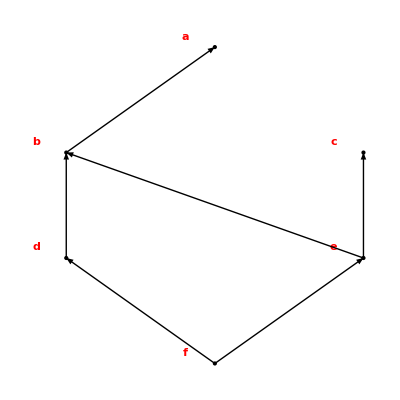

Diagrama de orden:

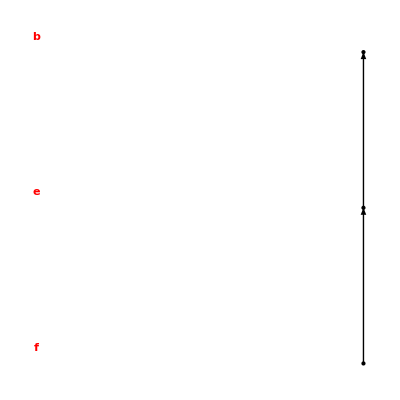

Diagrama de orden:

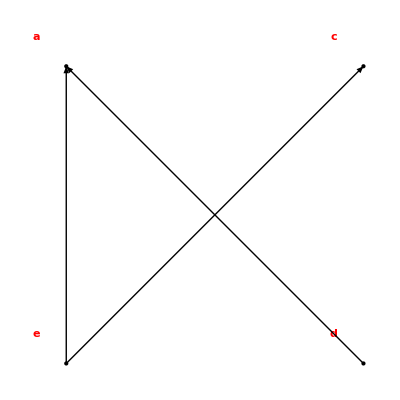

```mathematica
X={"a","b","c","d","e","f"};
Y={"b","f","e"};
Z={"c","a","e","d"};
R={{"f","f"},{"f","e"},{"f","d"},{"f","c"},{"f","b"},{"f","a"},{"e","e"},{"e","b"},{"e","c"},{"e","a"},{"b","b"},{"b","a"},{"d","d"},{"d","b"},{"d","a"},{"a","a"},{"c","c"}};
DIAGRAMA[A_,R_]:=Module[{B,t1,nivel,R1,tabla,puntos,k1,minimales,minimal,cont,Rlocal},
Clear[Coord];
tabla=Table[0,{i1,Length[A]},{j1,3}];
Rlocal = R;
B=A;
t1=1;
nivel=0;
While[B≠{},minimales={};nivel++;
Do[minimal=True;
Do[If[Intersection[{{B[[m1]],B[[n1]]}},Rlocal]≠{}&&n1≠m1,minimal=False];,{m1,1,Length[B]}];
If[minimal,AppendTo[minimales,B[[n1]]];
tabla[[t1]]={nivel,B[[n1]],0};
t1++;];,{n1,1,Length[B]}];
B=Complement[B,minimales];];
R1={};
Do[AppendTo[R1,{A[[i1]],A[[i1]]}],{i1,1,Length[A]}];
Rlocal=Complement[Rlocal,R1];
R1={};
Do[Do[If[Length[Intersection[Rlocal,{{Rlocal[[k1,1]],A[[j1]]},{A[[j1]],Rlocal[[k1,2]]}}]]==2,R1=Union[R1,{Rlocal[[k1]]}];];,{j1,1,Length[A]}],{k1,1,Length[Rlocal]}];
Rlocal=Complement[Rlocal,R1];
puntos={};t1=0;
Do[cont=0;
Do[If[tabla[[i1,1]]==j1,cont=cont+1],{i1,1,Length[A]}];
Do[t1++;
puntos=Union[puntos,{Text[Style[tabla[[t1,2]],Large,Bold,Red,Background->None,FontFamily->Times],{k1-(cont/2)-.1,j1+.1}],Point[{k1-(cont/2),j1}]}];
tabla[[t1,3]]=k1-(cont/2);,{k1,1,cont}],{j1,1,tabla[[Length[A],1]]}];
Coord[elem_]:=Do[If[elem==tabla[[h1,2]],Coord[elem]={tabla[[h1,3]],tabla[[h1,1]]}],{h1,1,Length[A]}];
Do[Coord[A[[i1]]],{i1,1,Length[A]}];
Do[AppendTo[puntos,Arrow[{Coord[Rlocal[[t1,1]]],Coord[Rlocal[[t1,2]]]}]];,{t1,1,Length[Rlocal]}];
Print["Diagrama de orden:"];
Show[Graphics[puntos],AspectRatio->1,Background->None]];
Cartesiano[A_,B_]:=Module[{cartesiano},cartesiano={};
Do[Do[AppendTo[cartesiano,{A[[i]],B[[j]]}],{i,1,Length[A]}];,{j,1,Length[B]}];Return[cartesiano]];
DIAGRAMA[X,R]
Ry={};
Do[If[Intersection[{R[[i]]},Cartesiano[Y,Y]]=={},Null,AppendTo[Ry,R[[i]]]];,{i,1,Length[R]}];
DIAGRAMA[Y,Ry]
Rz={};
Do[If[Intersection[{R[[i]]},Cartesiano[Z,Z]]=={},Null,AppendTo[Rz,R[[i]]]];,{i,1,Length[R]}];
DIAGRAMA[Z,Rz]
```